```mathematica
ω:= (λ/(l(l+1)))^(1/4)
Subscript[r, 0]:= (-1/(4 ω^2)+√(1/(16 ω^2)+ ω^6/(1728 λ^3)))^(1/3)+ (-1/(4 ω^2)- √(1/(16 ω^2)+ ω^6/(1728 λ^3)))^(1/3)
l= {1,2,3,4};
Print[Subscript[r, 0]]
```

{(-√(1/(3456 √2 λ^(3/2))+1/(8 √2 √λ))-1/(2 √2 √λ))^(1/3)+(√(1/(3456 √2 λ^(3/2))+1/(8 √2 √λ))-1/(2 √2 √λ))^(1/3),(-√(1/(10368 √6 λ^(3/2))+(√(3/2))/(8 √λ))-(√(3/2))/(2 √λ))^(1/3)+(√(1/(10368 √6 λ^(3/2))+(√(3/2))/(8 √λ))-(√(3/2))/(2 √λ))^(1/3),(-√(1/(41472 √3 λ^(3/2))+(√3)/(8 √λ))-(√3)/(2 √λ))^(1/3)+(√(1/(41472 √3 λ^(3/2))+(√3)/(8 √λ))-(√3)/(2 √λ))^(1/3),(-√(1/(69120 √5 λ^(3/2))+(√5)/(8 √λ))-(√5)/(2 √λ))^(1/3)+(√(1/(69120 √5 λ^(3/2))+(√5)/(8 √λ))-(√5)/(2 √λ))^(1/3)}

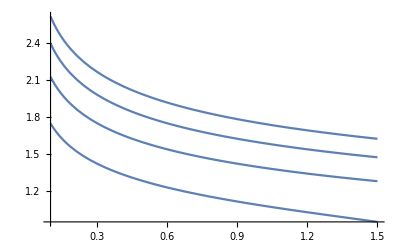

```mathematica
Plot[Im[Subscript[r, 0]],{λ, 0.1,1.5}]
```